```mathematica
(*num of trials*)
num=100000;
nSamples=2;
(*num of recombinations per base per gen*)
pi=1*^-7;
(*pi=1e-7/gen/base*)
sequenceLength=5000;
(* R=1e-3/gen*)
populationSize=20000;
(* T=10/gen (~1/gen) *)
parameterS = 2pi*sequenceLength*populationSize;
(* S = 20*)
```

### Prediction

#### F(τ)=exp(-S/2 τ^2-τ),exp(-aS/2 τ^2-bτ)

#### P(τ)=(Sτ+1)exp(-S/2 τ^2-τ),(aSτ+b)exp(-aS/2 τ^2-bτ)

```mathematica
predictionFree[tau_,alpha_,beta_]:=(alpha*parameterS*tau+beta)*Exp[-(alpha*parameterS)/2 tau^2-beta*tau]
```

```mathematica
Manipulate[Plot[predictionFree[tau,alpha,beta],{tau,0,2}],{{alpha,1},0.5,1.5},{{beta,1},0.5,1.5}]
```

### NonlinearModelFit

```mathematica
(*histdata = Transpose[StringReplace[Import["~/Emory/Research/Coalescent_Theory/zhao/sim_hist.txt"],{"["->"{","]"->"}"}]];*)
histdata=Transpose[Interpreter[DelimitedSequence[DelimitedSequence["Number",{"[",", ","]"}],{"[",", ","]"}]][Import["~/Emory/Research/Coalescent_Theory/zhao/2mrca/sim_hist.txt"]]];
```

```mathematica
fit=NonlinearModelFit[histdata,predictionFree[tau,alpha,beta],{alpha,beta},tau];
```

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
alpha | 0.731512 | 0.00867701 | 84.3046 | 4.25498×10^-157
beta | 1.28224 | 0.0204837 | 62.5981 | 1.97252×10^-132

```mathematica
predictionFixed[tau_]:=predictionFree[tau,1,1]
```

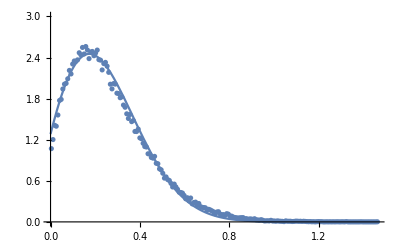

```mathematica
Show[ListPlot[histdata,PlotRange->{0,3}],Plot[fit[tau],{tau,0,Max[Transpose[histdata][[1]]]}],Plot[prediction[tau],{tau,0,Max[Transpose[histdata][[1]]]}]]
```

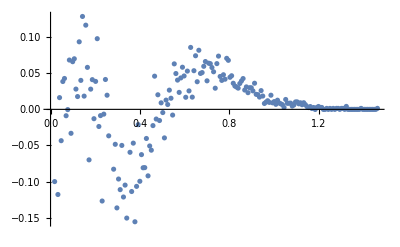

```mathematica
errorsAfter = histdata;
Do[errorsAfter[[idx,2]]=errorsAfter[[idx,2]]-fit[errorsAfter[[idx,1]]],{idx,Length[errorsAfter]}]
ListPlot[errorsAfter]
```

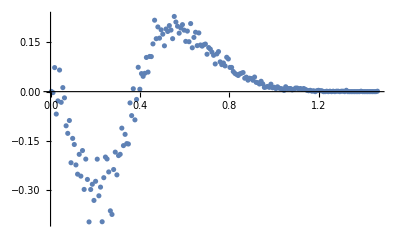

```mathematica
errorsBefore = histdata;
Do[errorsBefore[[idx,2]]=errorsBefore[[idx,2]]-predictionFixed[errorsBefore[[idx,1]]],{idx,Length[errorsBefore]}]
ListPlot[errorsBefore]
```